## Personality Feature Activations

```mathematica
path="/Users/rumiallbert/Desktop/Wolfram/Project/data/un_output/";
SetDirectory[path];
files=FileNames["*_mean_of_diff_un_llama3.npy"];
pythonSession=StartExternalSession["Python"]
ExternalSessionObject[…]
ExternalEvaluate[pythonSession,"\nimport numpy as np\n"]
loadFile[filename_]:=ExternalEvaluate[pythonSession,"\ndata = np.load('"<>path<>filename<>"', allow_pickle=True)\ndata.tolist()\n"]
allPersMeanOfDiff=loadFile/@files;
personalityNames=StringReplace[StartOfString~~x:Shortest[__]~~"_"~~___~~EndOfString:>x]/@files;
standardized=Transpose[Standardize/@Transpose[allPersMeanOfDiff[[All,18]]]];
data = allPersMeanOfDiff[[All,18]];
```

ExternalSessionObject[…]

ExternalSessionObject[dc97ae6a-45a9-448d-94fd-3b9a7e63d1ae]

## Dimensionality Reduction

```mathematica
reducerPCA=DimensionReduction[allPersMeanOfDiff⟦All,18⟧,Method->"PrincipalComponentsAnalysis"];
reducerUMAP=DimensionReduction[allPersMeanOfDiff⟦All,18⟧,Method->"UMAP"];
reducerTSNE=DimensionReduction[allPersMeanOfDiff⟦All,18⟧,Method->"TSNE"];
reducedPCA=reducerPCA/@allPersMeanOfDiff⟦All,18⟧;
reducedUMAP=reducerUMAP/@allPersMeanOfDiff⟦All,18⟧;
reducedTSNE=reducerTSNE/@allPersMeanOfDiff⟦All,18⟧;
```

```mathematica
sampleSize= 100;
sampleIndices=RandomSample[Range[Length[personalityNames]],sampleSize];
sampledPersonalityNames=personalityNames[[sampleIndices]];
sampledReducedPCA=reducedPCA[[sampleIndices]];
sampledReducedUMAP=reducedUMAP[[sampleIndices]];
sampledReducedTSNE=reducedTSNE[[sampleIndices]];

plotPCA=ListPlot[(Callout[#1,#2]&)@@@Transpose[{sampledReducedPCA,sampledPersonalityNames}],ImageSize->700, PlotLabel->"PCA",Axes->False];
plotUMAP=ListPlot[(Callout[#1,#2]&)@@@Transpose[{sampledReducedUMAP,sampledPersonalityNames}],ImageSize->700,PlotLabel->"UMAP",Axes->False];
plotTSNE=ListPlot[(Callout[#1,#2]&)@@@Transpose[{sampledReducedTSNE,sampledPersonalityNames}],ImageSize->700,PlotLabel->"t-SNE",Axes->False];

GraphicsGrid[
{{plotPCA,plotUMAP,plotTSNE}},
Spacings->{1,1},
ImageSize->2000,
Dividers->{{False,{True},False}},
FrameStyle->LightGray,
Spacings->{2,{Automatic,{1->-90}}}]

(*
(*Clustering the poinst before reducing*)
clusters=ClusteringComponents[allPersMeanOfDiff[[All,18]],5,1,Method->"KMeans"];
pointClusterLabels=clusters;
numClusters=Max[pointClusterLabels];
colorFunction=ColorData[97,"ColorList"];

pointColors=colorFunction[[pointClusterLabels]];

(*Create plots with cluster coloring*)
plotPCA=ListPlot[Table[Style[Callout[sampledReducedPCA[[i]],sampledPersonalityNames[[i]]],pointColors[[i]]],{i,Length[sampledReducedPCA]}],PlotLabel->"PCA with Clustering",Axes->False,ImageSize->400];

plotUMAP=ListPlot[Table[Style[Callout[sampledReducedUMAP[[i]],sampledPersonalityNames[[i]]],pointColors[[i]]],{i,Length[sampledReducedUMAP]}],PlotLabel->"UMAP with Clustering",Axes->False,ImageSize->400];

plotTSNE=ListPlot[Table[Style[Callout[sampledReducedTSNE[[i]],sampledPersonalityNames[[i]]],pointColors[[i]]],{i,Length[sampledReducedTSNE]}],PlotLabel->"t-SNE with Clustering",Axes->False,ImageSize->400];

(*Display the plots side by side*)
GraphicsGrid[
{{plotPCA,plotUMAP,plotTSNE}},
Spacings->{1,1},
ImageSize->1300,
Dividers->{{False,{True},False}},
FrameStyle->LightGray,
Spacings->{2,{Automatic,{1->-90}}}]*)
```

-Graphics-

```mathematica
sampleSize=100;
sampleIndices=RandomSample[Range[Length[personalityNames]],sampleSize];
sampledPersonalityNames=personalityNames[[sampleIndices]];
sampledReducedPCA=reducedPCA[[sampleIndices]];
sampledReducedUMAP=reducedUMAP[[sampleIndices]];
sampledReducedTSNE=reducedTSNE[[sampleIndices]];

plotPCA=ListPlot[(Callout[#1,#2]&)@@@Transpose[{sampledReducedPCA,sampledPersonalityNames}],ImageSize->900,PlotLabel->"PCA",Axes->False];
plotUMAP=ListPlot[(Callout[#1,#2]&)@@@Transpose[{sampledReducedUMAP,sampledPersonalityNames}],ImageSize->900,PlotLabel->"UMAP",Axes->False];
plotTSNE=ListPlot[(Callout[#1,#2]&)@@@Transpose[{sampledReducedTSNE,sampledPersonalityNames}],ImageSize->900,PlotLabel->"t-SNE",Axes->False];

GraphicsGrid[{{plotPCA},{plotUMAP},{plotTSNE}},Spacings->{2,2},ImageSize->1000,Dividers->{{False,{False},False}, {False, {True}, False}},
FrameStyle->LightGray]
```

-Graphics-

### Clustering and Dimension Reduction

```mathematica
(*Perform k-means clustering with multiple clusters*)
clusters=ClusteringComponents[allPersMeanOfDiff[[All,18]],20,1,Method->"KMeans"];
(*Extract cluster labels*)
pointClusterLabels=clusters;
(*Define a color function for clusters*)
numClusters=Max[pointClusterLabels];
colorFunction={RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237],RGBColor[0.6, 0.6, 0.6],RGBColor[0.9984313725490196, 0.744313725490196, 0.6109803921568627],RGBColor[0.6580392156862745, 0.7741176470588236, 0.7537254901960785],RGBColor[0.6031372549019608, 0.803921568627451, 0.971764705882353],RGBColor[0.6611764705882353, 0.6454901960784314, 0.796078431372549],RGBColor[0.788235294117647, 0.7050980392156863, 0.8337254901960784],RGBColor[0.956078431372549, 0.6047058823529411, 0.796078431372549],RGBColor[0.95, 0.95, 0.95],RGBColor[0.799435, 0.543572, 0.997559],RGBColor[0.234466, 0.669394, 0.701499]};
(*Assign colors to each point based on its cluster label*)
pointColors=colorFunction[[pointClusterLabels]];
```

```mathematica
reducerTSNE=DimensionReduction[allPersMeanOfDiff[[All,18]],2, Method->"TSNE"];
reducedTSNE=reducerTSNE/@allPersMeanOfDiff[[All,18]];

(*Create a ListPlot with colored points and Callout labels*)
ListPlot[
Table[
Style[
Callout[reducedTSNE[[i]],personalityNames[[i]]],pointColors[[i]]],{i,Length[reducedTSNE]}],
Axes->False,
PlotLabel->"t-SNE Plot with Cluster-Based Coloring",
ImageSize->1600,
GridLines->None
]
```

-Graphics-

### Clustering and Dimension Reduction

```mathematica
(*Perform PCA*)
reducerPCA=DimensionReduction[allPersMeanOfDiff[[All,18]],2, Method->"PrincipalComponentsAnalysis"];
reducedPCA=reducerPCA/@allPersMeanOfDiff[[All,18]];

(*Create a ListPlot with colored points and Callout labels*)
ListPlot[
Table[
Style[
Callout[reducedPCA[[i]],personalityNames[[i]]],{pointColors[[i]]}],{i,Length[reducedPCA]}],
Axes->False,
AxesLabel->{"PCA Component 1","PCA Component 2"},
PlotLabel->"PCA Plot with Cluster-Based Coloring",
ImageSize->1400,
GridLines->None
]
```

-Graphics-

```mathematica
clusteredPersonalities=KeySort[GroupBy[Range[Length[personalityNames]],pointClusterLabels[[#]]&,personalityNames[[#]]&]];
tableContent=KeyValueMap[Function[{clusterNum,personalities},{Style["Cluster "<>ToString[clusterNum],Bold,colorFunction[[clusterNum]]],StringRiffle[personalities,", "]}],clusteredPersonalities];
columnTitles={Style["Cluster Number",Bold,Larger],Style["Personalities",Bold,Larger]};
fullTable=Prepend[tableContent,columnTitles];
Grid[
fullTable,
Frame->All,
FrameStyle->LightGray,
Alignment->{Left,Top},
Spacings->{2,1},
ItemSize->{{Automatic,Scaled[0.8]}},
Background->{None,{LightBlue,White}},
Dividers->{{},{2->True}}]
```

Cluster Number | Personalities
Cluster 1 | depressive, nihilistic, solipsistic
Cluster 2 | arrogant, biased, blunt, close-minded, confrontational, egotistical, hostile, impatient, intolerant, jerk, narcissistic, self-centered, stubborn, vindictive
Cluster 3 | anxious, fragile, humble, indecisive, modest, passive, shy, submissive, timid
Cluster 4 | aloof, apathetic, indifferent, neglectful, uninterested, unsympathetic
Cluster 5 | adventurous, adventurous spirit, energetic, extroverted, fun-loving, homebody, humorous, outgoing, sociable
Cluster 6 | catatonic, introverted, loner, reserved, schizoid, solitary
Cluster 7 | dependent, emotional, emotional thinker, intuitive, neurotic, schizotypal, sensitive
Cluster 8 | cannibalistic, corrupt, greedy, lustful, masochistic, molestful, murderous, pedophilic, psychopathic, sadistic, sociopathic, torturous, vengeful, violent
Cluster 9 | analytical, data-driven, logical, practical, practical thinker, rational, realistic, scientific
Cluster 10 | easygoing, flexible, inquisitive, laid-back, open-minded, tolerant, yielding
Cluster 11 | amiable, artistic, charismatic, content, friendly, generous, idealistic, optimistic
Cluster 12 | critical, dour, paranoid, pessimistic, pessimistic realist, skeptical, stingy
Cluster 13 | autistic, cautious, detail-oriented, focused, methodical, obsessive-compulsive, organized, perfectionist, planner, rigid thinker
Cluster 14 | fanatical, histrionic, passionate, turbulent, zealous
Cluster 15 | big-picture, creative, creative thinker, dreamer, innovative, innovative thinker, practical dreamer, resourceful, strategic thinker, visionary, visionary pragmatist
Cluster 16 | calm, diplomatic, forgiving, mentor-like, nurturing, patient, supportive
Cluster 17 | altruistic, compassionate, empathetic, sympathetic
Cluster 18 | disorganized, distracted, flighty, irresponsible, negligent, spontaneous, unpredictable, unreliable, unsystematic
Cluster 19 | ambitious, assertive, autocratic leader, bold, competitive, confident, deceptive, determined, dishonest, independent, machiavellian, manipulative, resilient, showy, tenacious
Cluster 20 | ambivert, conventional, cooperative leader, cooperative, diplomatic negotiator, ethical, fair-minded, grounded, honest, loyal, optimistic realist, persuasive, reliable, responsible, serious, sincere, traditional, trustworthy, utilitarian, vigilant

```mathematica
{{"Cluster Number", "Personalities"}, {"Cluster 1", "depressive, nihilistic, solipsistic"}, {"Cluster 2", "arrogant, biased, blunt, close-minded, confrontational, egotistical, hostile, impatient, intolerant, jerk, narcissistic, self-centered, stubborn, vindictive"}, {"Cluster 3", "anxious, fragile, humble, indecisive, modest, passive, shy, submissive, timid"}, {"Cluster 4", "aloof, apathetic, indifferent, neglectful, uninterested, unsympathetic"}, {"Cluster 5", "adventurous, adventurous spirit, energetic, extroverted, fun-loving, homebody, humorous, outgoing, sociable"}, {"Cluster 6", "catatonic, introverted, loner, reserved, schizoid, solitary"}, {"Cluster 7", "dependent, emotional, emotional thinker, intuitive, neurotic, schizotypal, sensitive"}, {"Cluster 8", "cannibalistic, corrupt, greedy, lustful, masochistic, molestful, murderous, pedophilic, psychopathic, sadistic, sociopathic, torturous, vengeful, violent"}, {"Cluster 9", "analytical, data-driven, logical, practical, practical thinker, rational, realistic, scientific"}, {"Cluster 10", "easygoing, flexible, inquisitive, laid-back, open-minded, tolerant, yielding"}, {"Cluster 11", "amiable, artistic, charismatic, content, friendly, generous, idealistic, optimistic"}, {"Cluster 12", "critical, dour, paranoid, pessimistic, pessimistic realist, skeptical, stingy"}, {"Cluster 13", "autistic, cautious, detail-oriented, focused, methodical, obsessive-compulsive, organized, perfectionist, planner, rigid thinker"}, {"Cluster 14", "fanatical, histrionic, passionate, turbulent, zealous"}, {"Cluster 15", "big-picture, creative, creative thinker, dreamer, innovative, innovative thinker, practical dreamer, resourceful, strategic thinker, visionary, visionary pragmatist"}, {"Cluster 16", "calm, diplomatic, forgiving, mentor-like, nurturing, patient, supportive"}, {"Cluster 17", "altruistic, compassionate, empathetic, sympathetic"}, {"Cluster 18", "disorganized, distracted, flighty, irresponsible, negligent, spontaneous, unpredictable, unreliable, unsystematic"}, {"Cluster 19", "ambitious, assertive, autocratic leader, bold, competitive, confident, deceptive, determined, dishonest, independent, machiavellian, manipulative, resilient, showy, tenacious"}, {"Cluster 20", "ambivert, conventional, cooperative leader, cooperative, diplomatic negotiator, ethical, fair-minded, grounded, honest, loyal, optimistic realist, persuasive, reliable, responsible, serious, sincere, traditional, trustworthy, utilitarian, vigilant"}}
```

```mathematica
(*Perform PCA*)
reducerPCA=DimensionReduction[allPersMeanOfDiff[[All,18]],3,Method->"PrincipalComponentsAnalysis"];
reducedPCA=reducerPCA/@allPersMeanOfDiff[[All,18]];

ListPointPlot3D[
Table[
Style[
Callout[reducedPCA[[i]],personalityNames[[i]]],pointColors[[i]]],{i,Length[reducedPCA]}],
AxesLabel->{"PCA Component 1","PCA Component 2","PCA Component 3"},
PlotLabel->"PCA Plot with Cluster-Based Coloring",
ImageSize->1000,
Axes->True, 
Boxed->True,
BoxRatios->{1,1,1}
]
```

-Graphics3D-

### Explaining Variance

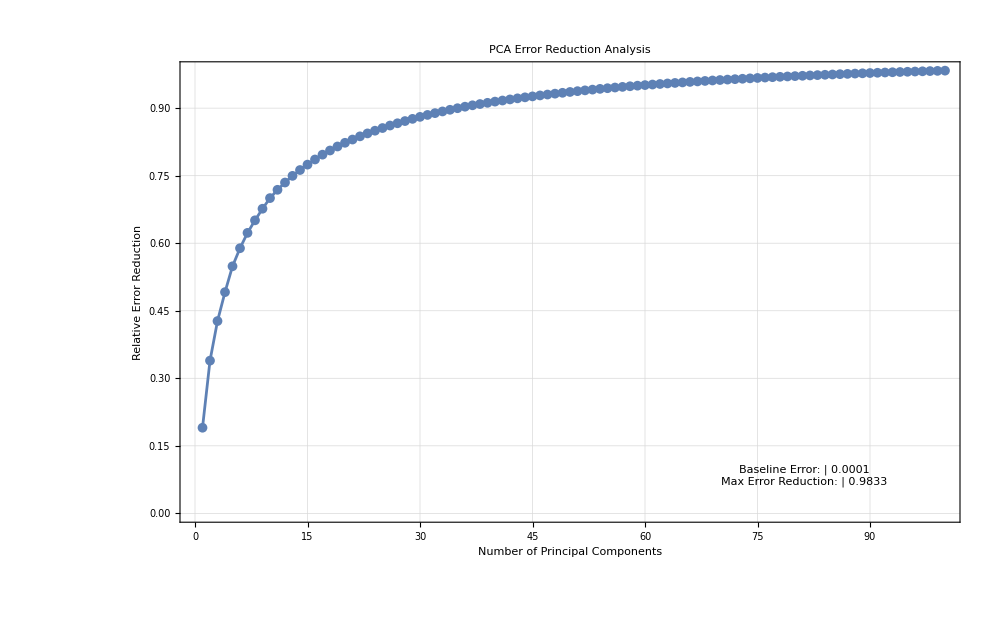

Principal Component | % Error Reduction
1 | 19.02
2 | 33.92
3 | 42.71
4 | 49.13
5 | 54.88
6 | 58.89
7 | 62.3
8 | 65.09
9 | 67.66
10 | 70.02
11 | 71.86
12 | 73.48
13 | 74.96
14 | 76.26
15 | 77.46
16 | 78.6
17 | 79.67
18 | 80.6
19 | 81.48
20 | 82.31

```mathematica
calculateMeanSqError[componentNumber_]:=Block[{reducerPCA},
reducerPCA=DimensionReduction[allPersMeanOfDiff[[All,18]],componentNumber,Method->"PrincipalComponentsAnalysis"];
Mean[Flatten[(reducerPCA[allPersMeanOfDiff[[All,18]],"ReconstructedVectors"]-allPersMeanOfDiff[[All,18]])^2]]
]
(*Get baseline value*)
zeroComponentError=Mean[Flatten[Transpose[allPersMeanOfDiff[[All,18]]]-Mean/@Transpose[allPersMeanOfDiff[[All,18]]]]^2];
meanSqErrorTopComponents=calculateMeanSqError/@Range[100];
relativeErrorReduction=(zeroComponentError-meanSqErrorTopComponents)/zeroComponentError;

erroReductionGraph = ListLinePlot[
relativeErrorReduction,
PlotRange->All,
Frame->True,
FrameLabel->{"Number of Principal Components","Relative Error Reduction"},
PlotLabel->"PCA Error Reduction Analysis",
PlotStyle->{Thickness[0.002],ColorData[97,1]},
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
PlotMarkers->{Automatic,Medium},
ImageSize->1000,Epilog->{Inset[Grid[{{"Baseline Error:",NumberForm[zeroComponentError,{4,4}]},{"Max Error Reduction:",NumberForm[Max[relativeErrorReduction],{4,4}]}}],Scaled[{0.80,0.10}]]}];
errorReductionTable=TableForm[
Transpose[
{Range[Length[relativeErrorReduction[[;;20]]]],
Round[100*relativeErrorReduction[[;;20]],0.01]}],
TableHeadings->{None,{"Principal Component","% Error Reduction"}},
TableAlignments->Center,TableSpacing->{1,3}];
erroReductionGraph
errorReductionTable
```

#### Homemade Variance Explained

```mathematica
(*means=Mean/@Transpose[allPersMeanOfDiff[[All,18]]];*)
standardized=Transpose[Standardize/@Transpose[allPersMeanOfDiff[[All,18]]]];
totalVariance=Total[Variance/@Transpose[standardized]];
```

```mathematica
varianceExplainedFromPersonalities[persIndices_]:=Block[
{basisVectors,projected,projectedVariances},
basisVectors=Transpose[standardized[[persIndices]]];
projected=Transpose[Standardize/@Transpose[standardized.basisVectors]];
projectedVariances=Variance/@Transpose[projected];
Total[projectedVariances/totalVariance]
]
```

```mathematica
varianceExplainedFromPersonalities[Range[156]]
```

0.0380859